# Demonstration : the origin of the power law

This notebook contains an illustration in the context of the following article, to appear in eLife in 2021:
Identical sequences found in distant genomes reveal frequent horizontal transfer across the bacterial domain
Michael Sheinman, Ksenia Arkhipova, Peter F. Arndt, Bas E. Dutilh, Rutger Hermsen, and Florian Massip.

Our goal here is to demonstrate the origin of the power-law tail of the match-length distributions (MLDs) discussed there, as illustrated in Box 1 of the main text

A single, long transfer between a pair of genomes a and b

Imagine that, due to an event of Horizontal Gene Transfer (HGT) a time t ago, a pair of genomes a and b share an exact match of length K.  Due to mutations in either instance of the sequence, occurring at a rate  2 μ, this long match is subsequently “broken” into an ever increasing number of smaller pieces (see Box 1).  Then after some time the contribution of this sequence to the absolute frequency distribution of exact matches between the genomes is well approximated by the following exponential distribution:

```mathematica
mldExp[r_, t_] := K (2 μ t)^2 E^(-2 μ r t)
```

The normalization of this equation is correct. Let us check this by integrating over r; that should result in the total number of matches (pieces of the stick):

```mathematica
numberOfSticks = Assuming[{t>0, μ>0},Integrate[mldExp[r,t], {r, 0, Infinity}]]
```

2 K t μ

The total number of matches increases linearly in time.

In addition, we can find the cumulative length of the pieces:

```mathematica
totalLength = Assuming[{t>0, μ>0},Integrate[ r mldExp[r,t], {r, 0, Infinity}]]
```

K

That is the total length of the matches stays constant at K, unchanged by the “breaking” of the matches.

A single transfer between genus 1 and genus 2

Now assume that a time t ago, a long sequence of length K is introduced in two genera 1 and 2, generating a long exact match between some genomes belonging to genus 1 and 2.  We assume that, due to a selective sweep, this sequence is later found in a fraction f_1 of genomes from genus 1 and in a fraction f_2 of genomes of genus 2. Now we sample n_1 genomes of genus 1 and n_2 of genus 2, and find all matches between all genome pairs (a, b) where a is in genus 1 and b is in genus 2.  Then, the expected contribution of this sequence to the absolute frequency distribution of all exact matches in the sample is:

```mathematica
mldExp2[r_, t_] := f1 f2 n1 n2 mldExp[r,t]
```

Many transfers between genus 1 and 2

Now we consider that such transfers have taken place many times in the past, at a constant rate ρ. Then the expected absolute frequency distribution becomes is a mixture of many events that occurred in the past. It is obtained by integrating over time:

```mathematica
mldCombined[r_] = Assuming[{t>0, μ>0, ρ>0, r>0},Integrate[ρ mldExp2[r, t], {t, 0, Infinity}]]
```

(f1 f2 K n1 n2 ρ)/(r^3 μ)

The result is a power law with exponent -3.  This shows that the power law result from an equal mixing of exponential MLDs.

Normalization of the MLD

In the main text, we present empirical MLDs that have been normalized by dividing the absolute frequencies by the total length of the genomes sampled from both genus 1 and genus 2, denoted l_1 and l_2.  This way, if we double the number of sequences sampled from one genus, the expected MLD stays the same, because both the absolute number of matches and the norm are expected to double.

Defining L_1=l_1/n_1 and L_2=l_2/n_2 as the mean length of the genomes in these genera, the definition of the normalized MLD becomes

```mathematica
nldCombinedNormalized[r_]=Simplify[mldCombined[r]/(L1 L2 n1 n2)]
```

(f1 f2 K ρ)/(L1 L2 r^3 μ)

That is the equation shown in the main text.

Demonstration of the emergence of the power law

The emergence of the power law can be demonstrated by randomly sampling 50 exponential MLDs and adding them up. The result should show a power law with exponent of -3.

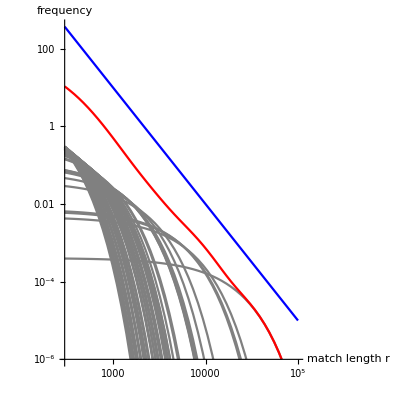

```mathematica
SeedRandom[12];  (* for reproducibility *)
number = 50; (* number of exponential MLDs sampled *)
sequenceLength = 50000;

(* pick random divergences μ t between 0 and 5*10^-3 by sampling times between 0 and 5*10^-3/μ *)
times= Sort[Table[RandomReal[{0,5 10^-3}],{i,1,number}]]/μ; 
(* generate the MLDs corresponding to this divergence *)
mldSample =Table[
Assuming[
μ>0, 
Simplify[
mldExp[r, times[[i]]
]
]/.{K->sequenceLength}], 
{i, 1, number,1}
];
(* sum them up *)
mldSum =Sum[mldSample[[i]], {i, 1, number}];

(* plot all MLDs, their sum, and a power law *)LogLogPlot[{mldSample,mldSum,  10^10/r^3}, {r, 300, 10^5}, PlotRange->{{3*10^2,10^5},{10^-6,All}}, 
AspectRatio->1,AxesStyle->Black, AxesLabel->{"match length r", "frequency"}, PlotStyle->Flatten[{Table[Gray, {i, 1, number}], Red, Blue}]]
```

Here, the gray lines are the individual exponential MLDs (in log-scale), the red line is their sum, and the blue line is a power law with exponent -3 (for comparison). This figure is the basis for the figure in Box 1.